## Q1

```mathematica
f[x_]= x Exp[-x] + x (1 - x);
```

```mathematica
points={0, 0.1, 0.2, 0.4, 0.8};
results=Evaluate[f/@points]
```

{0,0.180484,0.323746,0.508128,0.519463}

## Q2

```mathematica
BesselJ[n, x]
```

BesselJ[n,x]

```mathematica
Manipulate[Plot[BesselJ[n,x],{x,0,21}],{n,1}]
```

```mathematica
s1=FindRoot[BesselJ[1,x]==0,{x,0}];
s2=FindRoot[BesselJ[1,x]==0,{x,3.8}];
s3=FindRoot[BesselJ[1,x]==0,{x,7}];
```

```mathematica
sol={s1,s2,s3}
```

{{x→0.},{x→3.83171},{x→7.01559}}

## Q3

```mathematica
integral=Integrate[Sin[x] Exp[-x],x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify@D[integral,x]
```

ⅇ^-x Sin[x]

## Q4

```mathematica
f= Exp[-ArcTan[x]];
 Simplify@PowerExpand@Normal@Series[f,{x,0,4}]
```

1-x+x^2/2+x^3/6-(7 x^4)/24

```mathematica
Simplify@PowerExpand@Normal@Series[f,{x,∞,4}]
```

(ⅇ^(-π/2) (-7-4 x+12 x^2+24 x^3+24 x^4))/(24 x^4)

## Q5

{{y→Function[{x},3^(2/3) AiryAi[x] Gamma[2/3]]}}

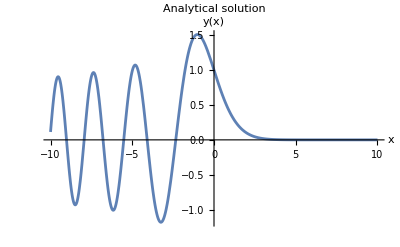

```mathematica
sol=DSolve[{y''[x]-x y[x]==0,y[0]==1,y'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]},y,{x,-10,10}]

Plot[y[x]/. sol,{x,-10,10},PlotRange->All,AxesLabel->{"x","y(x)"},PlotLabel->"Analytical solution"]
```

```mathematica
Clear[y,x]
```

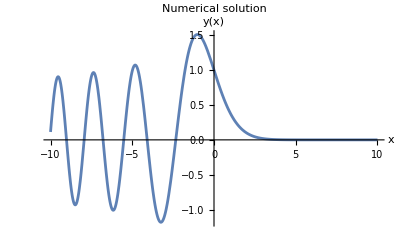

```mathematica
soln=NDSolve[{y''[x]-x y[x]==0,y[0]==1,y'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]},y,{x,-10,10},Method->"ImplicitRungeKutta",AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity];
ynum=(y/.Flatten@soln)[x];
Plot[ynum,{x,-10,10},PlotRange->All,AxesLabel->{"x","y(x)"},PlotLabel->"Numerical solution"]
```